```mathematica
Item[KeyEvent["j",Modifiers->{Control,Shift}],KernelExecute[Remove["Global`*"]],MenuEvaluator->Automatic];

Map[SetOptions[#,Prolog->{{EdgeForm[],Texture[{{{0,0,0,0}}}],Polygon[#,VertexTextureCoordinates->#]&[{{0,0},{1,0},{1,1}}]}}]&,{Graphics3D,ContourPlot3D,ListContourPlot3D,ListPlot3D,Plot3D,ListSurfacePlot3D,ListVectorPlot3D,ParametricPlot3D,RegionPlot3D,RevolutionPlot3D,SphericalPlot3D,VectorPlot3D}];

μ=3.5× 10^-5;
γ=0.2;
a=0.02;

legendSize=10;  
legendTextSize=10; 

beta1[b_]:=(γ+μ-a)/2+Sqrt[γ^2 (γ+μ+a)^2+4 b γ (γ+μ)^2]/(2 γ);
beta2[b_]:=1/(2 γ) (-a γ+2 b γ+γ^2+γ μ+Sqrt[γ (a^2 γ+4 b^2 γ+4 b μ (γ+μ)+γ (γ+μ)^2+2 a γ (-2 b+γ+μ))]);

g[β_]=Piecewise[{{β+a,β<beta1[b]},{(β+a)/2+(b(γ+μ)^2)/(2γ(β-(μ+γ))),beta1[b]≤β≤beta2[b]},{β+a-b,β>beta2[b]}}];

pmax[β_]=Piecewise[{{0.,β<beta1[b]},{(β+a)/(2b)-(γ+μ)^2/(2γ(β-(μ+γ))),beta1[b]≤β≤beta2[b]},{1.,β>beta2[b]}}];
table1=Table[Flatten[Take[Table[NestList[g,0.201+k*0.001,1000]/. c_Real->{b,c}(*covid*),{b,0.0201,0.215,0.0005}],All,{950,1000,1}],1],{k,10}];
table2=Table[Flatten[Take[Table[MapAt[pmax,NestList[g,0.201+k*0.001,1000],All]/. c_Real->{b,c}(*covid*),{b,0.0201,0.215,0.0005}],All,{950,1000,1}],1],{k,10}];
p1=ListPlot[table1,PlotStyle->Directive[Opacity[0.2],PointSize[0.002], ColorData["Crayola"]["Denim"]],Frame->True,Axes->False,FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->{{Thickness[0],Thickness[0]},{Thickness[0],Thickness[0]}}];

GAScond=Max[a,(3 (-a^2 γ+4 γ^3+8 γ^2 μ+4 γ μ^2))/(16 (γ+μ)^2),(3 γ (-a+γ+μ)^2)/(4 (γ+μ)^2)];
LAScond=Max[a,(3 γ (-a+γ+μ)^2)/(4 (γ+μ)^2)];

fixedpoint[b_]:=(γ+μ+a)/2+Sqrt[γ a (a-2 (γ+μ))+(4 b+γ) (γ+μ)^2]/(2 Sqrt[γ]);
ming[b_]:=(γ+μ+a)/2+Sqrt[b γ (γ+μ)^2]/γ;

betamin[b_]:=Piecewise[{{γ+μ+Sqrt[b γ (γ+μ)^2]/γ,b>(γ+μ+a)/2},{beta2[b],a<b≤(γ+μ+a)/2}}];


lineLAS=Graphics[{ColorData["Crayola"]["PurplePizzazz"],Thickness->0.001,Line[{{LAScond,0.22},{LAScond,0.346}}],Text[Style[Column[{"LAS","Condition"},Center,Spacings->0.2],Bold,(*10*)10],{LAScond,0.35},Offset[{-200,10},{LAScond,0.346}]  ]}];



lineGAScond=Graphics[{ColorData["Crayola"]["SunsetOrange"],Thickness->0.001,Line[{{GAScond,0.22},{GAScond,0.346}}],Text[Style[Column[{"GAS","Condition"},Center,Spacings->0.2],Bold,10],{GAScond,0.35},Offset[{-200,10},{GAScond,0.346}]]}];



p4=Plot[fixedpoint[b],{b,0.0201,0.22},PlotRange->All,PlotStyle->Directive[ColorData["Crayola"]["Razzmatazz"],Thickness->0.003,Dashing[{0.003,0.005}]],PlotLegends->SwatchLegend[{"fixed point"},LegendMarkerSize->legendSize,LabelStyle->{FontSize->legendTextSize}],LabelStyle->Directive[FontSize->5]];



p6=Plot[g[beta1[b]]+0.0007,{b,0.0201,0.22},PlotRange->All,PlotStyle->Directive[Thickness->0.003,ColorData["Crayola"]["Black"]],PlotLegends->SwatchLegend[{Column[{"lower bound \!\(\*SubscriptBox[\(β\), \(-\)]\)","upper bound \!\(\*SubscriptBox[\(β\), \(+\)]\)"},Alignment->Center,Spacings->1]},LegendMarkerSize->legendSize,LabelStyle->{FontSize->legendTextSize}],LabelStyle->Directive[FontSize->5]];


betaminus[b_]:=Piecewise[{{g[g[beta1[b]]],g[beta1[b]]<betamin[b]},{g[betamin[b]],g[beta1[b]]≥betamin[b]}}];



p9=Plot[betaminus[b]-0.0007,{b,0.0201,0.215},PlotRange->All,PlotStyle->Directive[Thickness->0.003,ColorData["Crayola"]["Black"]],AxesLabel->{"b","β minus adjustment"},LabelStyle->{FontFamily->"Helvetica",FontSize->10,Black}  ];


criticalcurves=Plot[{Drop[NestList[g,beta1[b],4],1], Drop[NestList[g,betamin[b],4],2]},{b,0.0201,0.215},PlotRange->All,PlotStyle->Directive[Thickness->0.0005,Blend[{ColorData["Crayola"]["Denim"],White},0.3]],LabelStyle->Directive[FontSize->15]];

plot1=Show[{p1,p4,p6,p9,lineLAS,lineGAScond,criticalcurves},PlotRange->{{0.0201,0.215},All},ImageSize->{2400/3.5,1800/3.5},LabelStyle->{FontFamily->"Helvetica",FontSize->10,Black},Frame->True,FrameLabel->{{"β_n",None},{"Bifurcation Parameter: b",None}}]

(*Export["bifdiagram.pdf",plot1];*)
```

-Graphics-

```mathematica
ColorData["Crayola","Panel"];
```

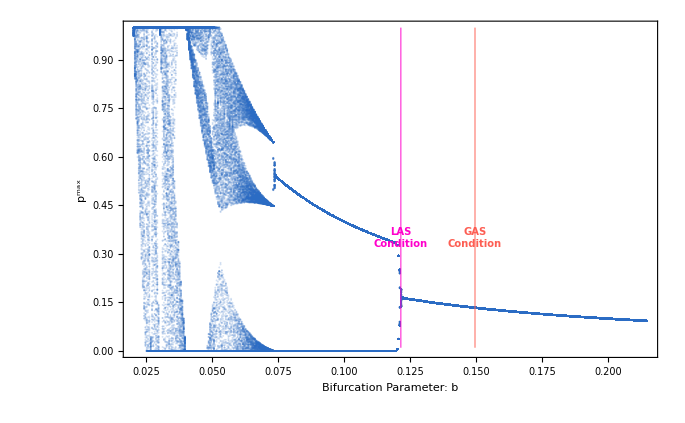

```mathematica
ppmax=ListPlot[table2,PlotStyle->Directive[Opacity[0.2],PointSize[0.002], ColorData["Crayola"]["Denim"]],Frame->True,Axes->False,FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->{{Thickness[0],Thickness[0]},{Thickness[0],Thickness[0]}}];
lineLASlong=Graphics[{ColorData["Crayola"]["PurplePizzazz"],Thickness->0.001,Line[{{LAScond,0.01},{LAScond,1}}],Text[Style[Column[{"LAS","Condition"},Center,Spacings->0.2],Bold,10],{LAScond,0.35},Offset[{-200,10},{LAScond,0.346}]  ]}];

lineGAScondlong=Graphics[{ColorData["Crayola"]["SunsetOrange"],Thickness->0.001,Line[{{GAScond,0.01},{GAScond,1}}],Text[Style[Column[{"GAS","Condition"},Center,Spacings->0.2],Bold,10],{GAScond,0.35},Offset[{-200,10},{GAScond,0.346}]]}];
plotpmax=Show[{ppmax,lineLASlong,lineGAScondlong},PlotRange->{{0.0201,0.215},All},ImageSize->{2400/3.5,1800/3.5},LabelStyle->{FontFamily->"Helvetica",FontSize->10,Black},Frame->True,FrameLabel->{{"p^max",None},{"Bifurcation Parameter: b",None}}]

(*Export["bifdiagramPmax.pdf",plotpmax];*)
```